-Graphics3D-

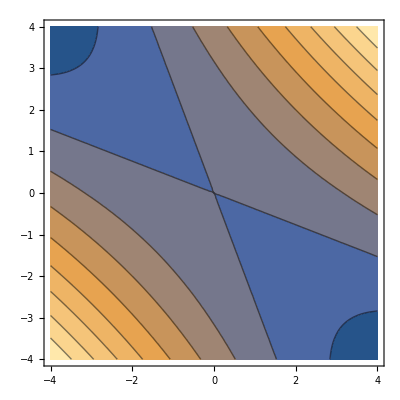

```mathematica
pm1 =Plot3D[ x^2+y^2+3 x y, {x,-4,4},{y,-4,4}]
pm2 =ContourPlot[ x^2+y^2+3 x y, {x,-4,4},{y,-4,4}]
```

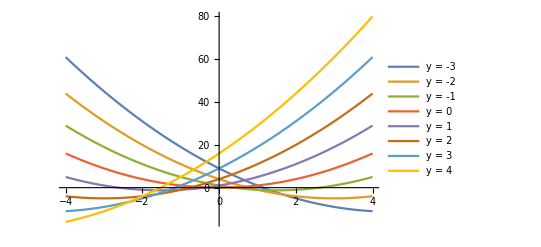

{-1,0,1,2}

```mathematica
Plot[ ((x^2+#^2+3 x # )&/@ (Range[8]-4)) // Evaluate, {x,-4,4}, PlotLegends-> (Row[{"y = ",#}]&/@(Range[8]-4))]
```

```mathematica
Module[{r=0.0001},Plot3D[ {x^3 y/(x^6 + y^2),y -x^3}// Evaluate, {x,-r,r},{y,-r,r}, PlotLegends -> "Expressions",PerformanceGoal->"Quality"]]
Module[{r=0.0001},Plot3D[ x^3 y/(x^6 + y^2), {x,-r,r},{y,-r,r},PerformanceGoal->"Quality"(*, PlotRange  -> Full*)]]
```

-Graphics3D-

-Graphics3D-

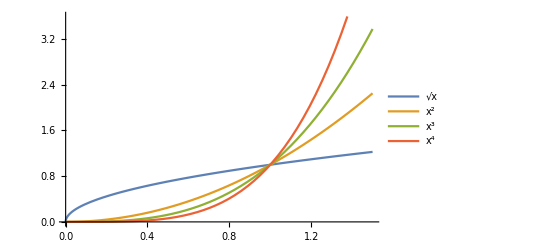

```mathematica
p = Plot[(x^# &/@ {1/2,2,3,4} ) // Evaluate,{x,0,1.5}, PlotLegends->Placed["Expressions", {Left,Top}]]
```

```mathematica
<< peeters`;
peeters`setGitDir["../project/figures/ece1505-convex-optimization"]
```

/Users/pjoot/project/figures/ece1505-convex-optimization

```mathematica
peeters`exportForLatex[ "l7xToTheNFig1", p]
```

{l7xToTheNFig1.eps,l7xToTheNFig1pn.png}

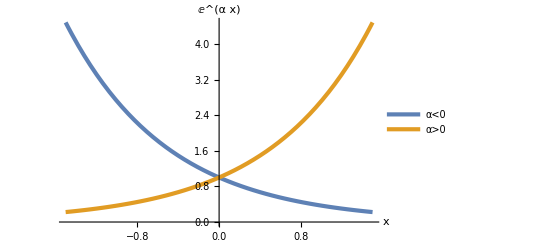

```mathematica
p2 = Plot[ (E^(# x) &/@ {-1,1}) // Evaluate, {x,-1.5,1.5},PlotLegends->Placed[{α <0,α >0}, {Right,Center}], Ticks -> None, AxesLabel->{x,E^(α x)}, PlotTheme-> "ThickLines"]
```

```mathematica
peeters`exportForLatex[ "l7eToAlphaXFig2", p2]
```

{l7eToAlphaXFig2.eps,l7eToAlphaXFig2pn.png}

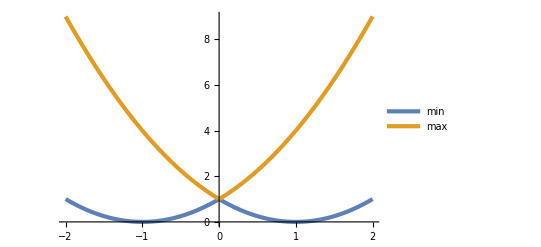

```mathematica
p4=Plot[((#[(x-1)^2,(x+1)^2])&/@ {Min,Max} ) // Evaluate, {x,-2,2}, PlotTheme-> "ThickLines",PlotLegends->Placed[{min,max}, {Right,Center}], Ticks -> None]
```

```mathematica
peeters`exportForLatex[ "l7minAndMaxFig4", p4]
```

{l7minAndMaxFig4.eps,l7minAndMaxFig4pn.png}

```mathematica
peeters`exportForLatex[ "l7quadratic3dFig7a", pm1]
peeters`exportForLatex[ "l7quadraticContourFig7b", pm2]
```

{l7quadratic3dFig7a.eps,l7quadratic3dFig7apn.png}

{l7quadraticContourFig7b.eps,l7quadraticContourFig7bpn.png}